ReplaceAll::reps: {#1} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

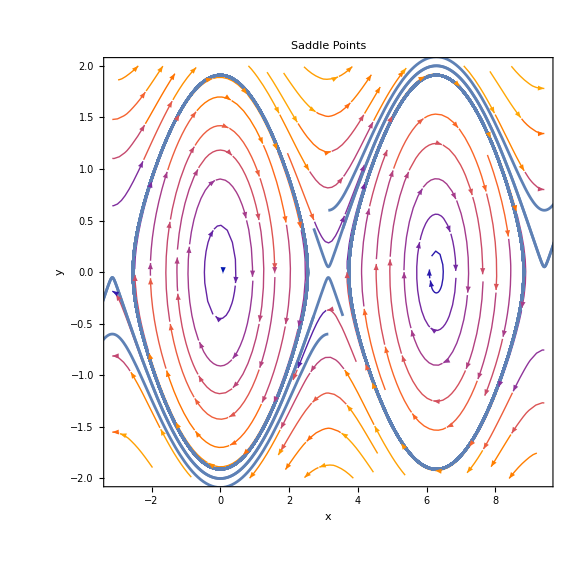

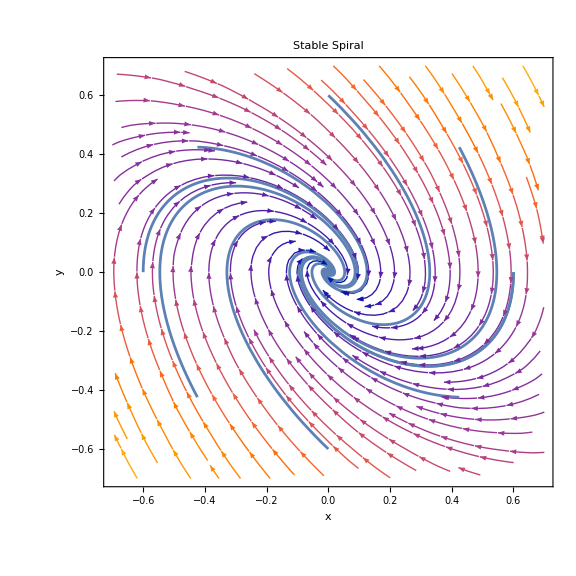

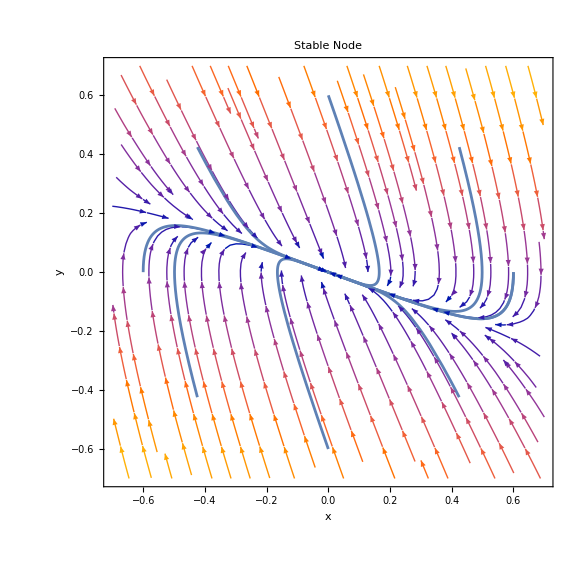

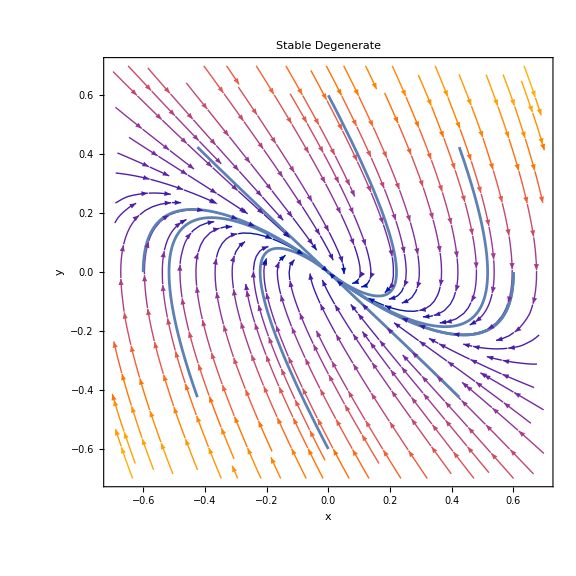

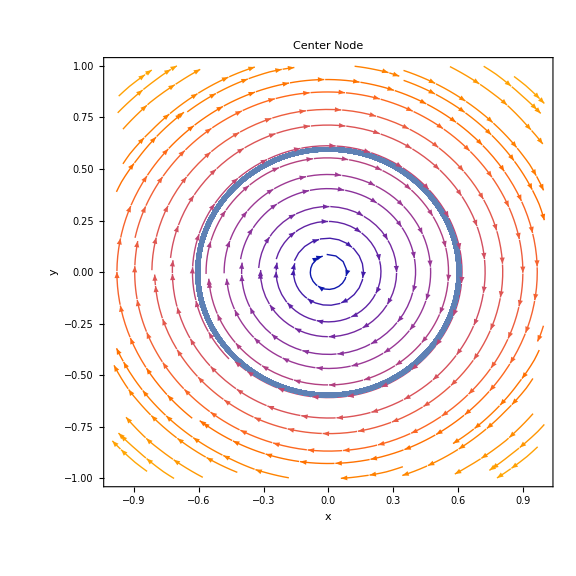

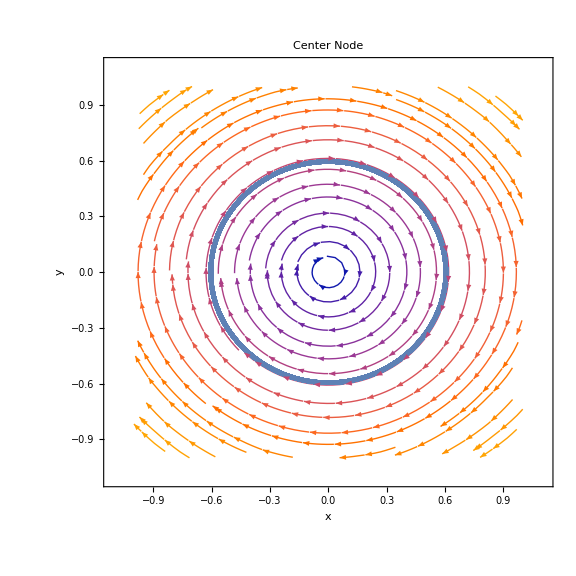

```mathematica
ClearAll["Global`*"]

(*Define fixed points*)
sp=0;
ss=1;
sn=3;
sdn=2;
cn=0;

(*Define differential equations*)
eq1=x'[t]==y[t];
eqSaddle=y'[t]==-Sin[x[t]]-sp*y[t];
eqStabSpir=y'[t]==-Sin[x[t]]-ss*y[t];
eqStabNode=y'[t]==-Sin[x[t]]-sn*y[t];
eqStabDeNode=y'[t]==-Sin[x[t]]-sdn*y[t];
eqCenter=y'[t]==-Sin[x[t]]-cn*y[t];

(*Define systems*)
saddle={eq1,eqSaddle};
stabSpiral={eq1,eqStabSpir};
stabNode={eq1,eqStabNode};
stabDeNode={eq1,eqStabDeNode};
center={eq1,eqCenter};

(*Define initial conditions*)
nTraj=8;
r1=0.6;
r2=0.3;

startPt1=Table[{x[0]==Pi+r1*Cos[2*Pi*i/nTraj],y[0]==r1*Sin[2*Pi*i/nTraj]},{i,0,nTraj}];
startPt2=Table[{x[0]==0+r1*Cos[2*Pi*i/nTraj],y[0]==r1*Sin[2*Pi*i/nTraj]},{i,0,nTraj}];
startPt3=Table[{x[0]==0+r2*i,y[0]==r2*i},{i,0,nTraj-1}];

(*Define time range*)
t0=0;
tMax=120;

(*Solve differential equations*)
sol1=Table[NDSolve[{saddle,sp},{x,y},{t,t0,tMax}],{sp,startPt1}];
sol21=Table[NDSolve[{stabSpiral,sp},{x,y},{t,t0,tMax}],{sp,startPt2}];
sol22=Table[NDSolve[{stabNode,sp},{x,y},{t,t0,tMax}],{sp,startPt2}];
sol23=Table[NDSolve[{stabDeNode,sp},{x,y},{t,t0,tMax}],{sp,startPt2}];
sol24=Table[NDSolve[{center,sp},{x,y},{t,t0,tMax}],{sp,startPt2}];

(*Create stream plots*)
sp1=StreamPlot[{y,-Sin[x]-sp*y},{x,-Pi,3*Pi},{y,-2,2},PlotRange->All];
sp21=StreamPlot[{y,-Sin[x]-ss*y},{x,-0.7,0.7},{y,-0.7,0.7},PlotRange->All];
sp22=StreamPlot[{y,-Sin[x]-sn*y},{x,-0.7,0.7},{y,-0.7,0.7},PlotRange->All];
sp23=StreamPlot[{y,-Sin[x]-sdn*y},{x,-0.7,0.7},{y,-0.7,0.7},PlotRange->All];
sp24=StreamPlot[{y,-Sin[x]-cn*y},{x,-1,1},{y,-1,1},PlotRange->All];

(*Plot trajectories*)
tp1=ParametricPlot[Evaluate[{x[t],y[t]}/. #]&/@sol1,{t,t0,tMax}];
tp21=ParametricPlot[Evaluate[{x[t],y[t]}/. #]&/@sol21,{t,t0,tMax}];
tp22=ParametricPlot[Evaluate[{x[t],y[t]}/. #]&/@sol22,{t,t0,tMax}];
tp23=ParametricPlot[Evaluate[{x[t],y[t]}/. #]&/@sol23,{t,t0,tMax}];
tp24=ParametricPlot[Evaluate[{x[t],y[t]}/. #]&/@sol24,{t,t0,tMax}];

(*Display the plots with labels*)
Show[sp1,tp1,FrameLabel->{"x","y"},PlotLabel->"Saddle Points"]
Show[sp21,tp21,FrameLabel->{"x","y"},PlotLabel->"Stable Spiral"]
Show[sp22,tp22,FrameLabel->{"x","y"},PlotLabel->"Stable Node"]
Show[sp23,tp23,FrameLabel->{"x","y"},PlotLabel->"Stable Degenerate"]
Show[sp24,tp24,FrameLabel->{"x","y"},PlotLabel->"Center Node"]
```